```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210210_impacts_in_time_windows"];
```

```mathematica
data=Import["data_with_time_windows.mx"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
Dimensions@DeleteDuplicates@data[[1]][[All,10]]
```

{80}

{33}

Width Feature

```mathematica
window=1;
rawaim=data[[window]][[All,9]];
aim=DeleteCases[rawaim,"NA"];
campaign=Delete[Delete[data[[window]][[All,2]],Position[rawaim,"NA"]],Position[aim,0]];
seri=Delete[Delete[data[[window]][[All,1]],Position[rawaim,"NA"]],Position[aim,0]];
aim=Delete[aim,Position[aim,0]];
Print["unique aim data members: ",Dimensions@DeleteDuplicates@aim]
Print["aim data length: ",Dimensions@aim]
Print["sequence data groups amount: ",Dimensions@DeleteDuplicates@campaign]
```

unique aim data members: {78}

aim data length: {40209}

sequence data groups amount: {122}

```mathematica
Sort@DeleteDuplicates@aim
```

{1060.,1070.,1080.,1090.,1110.,1130.,1140.,1150.,1170.,1180.,1190.,1200.,1210.,1220.,1230.,1240.,1250.,1260.,1270.,1280.,1290.,1300.,1310.,1320.,1330.,1340.,1350.,1360.,1370.,1380.,1390.,1400.,1410.,1420.,1430.,1440.,1450.,1460.,1470.,1480.,1490.,1500.,1510.,1520.,1530.,1540.,1550.,1560.,1570.,1580.,1590.,1600.,1610.,1620.,1630.,1640.,1650.,1660.,1670.,1700.,1710.,1720.,1730.,1740.,1750.,1760.,1770.,1780.,1790.,1800.,1810.,1820.,1830.,1840.,1850.,1860.,1870.,1880.}

```mathematica
range=Range[Min@Cases[Sort@DeleteDuplicates@aim,Except@0],Max@Sort@DeleteDuplicates@aim];
check=Flatten@Table[Mod[Dimensions@aim,i],{i,range}];
Print["Minimum Remainder: ",min=Min[check]]
pos=Position[check,min][[1]];
Print["Bucket Size: ",bucketsize=(Rationalize@range)[[pos]]]
```

Minimum Remainder: 1.

Bucket Size: {1436}

```mathematica
bins=Table[MinMax[i],{i,Partition[Sort[aim],bucketsize]}]
```

{{1060.,1220.},{1220.,1220.},{1220.,1220.},{1220.,1230.},{1230.,1230.},{1230.,1230.},{1230.,1240.},{1240.,1290.},{1290.,1380.},{1380.,1430.},{1430.,1500.},{1500.,1520.},{1520.,1530.},{1530.,1530.},{1530.,1530.},{1530.,1530.},{1530.,1540.},{1540.,1540.},{1540.,1540.},{1540.,1560.},{1560.,1600.},{1600.,1740.},{1740.,1840.},{1840.,1840.},{1840.,1840.},{1840.,1850.},{1850.,1850.},{1850.,1880.}}

```mathematica
binning=Table[Catch[Do[If[IntervalMemberQ[Interval[i],aim[[j]]]==True,Throw[i]],
{i,bins}]],{j,Length[aim]}];
Position[binning,Null]
```

{}

```mathematica
aim=binning;
binningmembers=Sort[DeleteDuplicates[aim]];
Print["binning amount: ",Dimensions@DeleteDuplicates@binning]
Print["dimension of binned data: ",Dimensions@aim]
Print["binning members dimension : ",Dimensions@binningmembers]
```

binning amount: {16,2}

dimension of binned data: {40209,2}

binning members dimension : {16,2}

```mathematica
(*part11=Take[Position[aim,{1220.10046386719,1222.64038085938}],1316];*)
part12=Take[Position[aim,{1220.10046386719,1222.64038085938}],{1317,2629}];
part13=Take[Position[aim,{1220.10046386719,1222.64038085938}],{2630,3942}];
part14=Take[Position[aim,{1220.10046386719,1222.64038085938}],-1313];
(*aim=ReplacePart[aim,part11->{"1220.1-1st","1222.64-1st"}];*)
aim=ReplacePart[aim,part12->{"1220.1-2nd","1222.64-2nd"}];
aim=ReplacePart[aim,part13->{"1220.1-3rd","1222.64-3rd"}];
aim=ReplacePart[aim,part14->{"1220.1-4th","1222.64-4th"}];

(*part21=Take[Position[aim,{1507.04553222656,1528.76245117188}],1256];*)
part22=Take[Position[aim,{1507.04553222656,1528.76245117188}],{1257,2510}];
part23=Take[Position[aim,{1507.04553222656,1528.76245117188}],{2511,3764}];
part24=Take[Position[aim,{1507.04553222656,1528.76245117188}],-1254];
(*aim=ReplacePart[aim,part21->{"1507.05-1st","1528.76-1st"}];*)
aim=ReplacePart[aim,part22->{"1507.05-2nd","1528.76-2nd"}];
aim=ReplacePart[aim,part23->{"1507.05-3rd","1528.76-3rd"}];
aim=ReplacePart[aim,part24->{"1507.05-4th","1528.76-4th"}];

(*{1449.38745117188,1497.01245117188}->2006,{1497.01245117188,1507.04553222656}->948*)
(*{1449.38745117188,1497.01245117188}->{1449.39,1450.02} 
{1497.01245117188,1507.04553222656}->{1450.02,1507.04}*)
part31=Take[Position[aim,{1449.38745117188,1497.01245117188}],-500];
part32=Position[aim,{1497.01245117188,1507.04553222656}];
part33=Take[Position[aim,{1449.38745117188,1497.01245117188}],1506];
aim=ReplacePart[aim,part31->{1450.02,1507.04}];
aim=ReplacePart[aim,part32->{1450.02,1507.04}];
aim=ReplacePart[aim,part33->{1449.39,1450.02}];
```

```mathematica
binningmembers=Sort[DeleteDuplicates[aim]]
```

{{713.316,1103.64},{1103.64,1220.1},{1220.1,1222.64},{1222.64,1227.46},{1227.46,1231.58},{1231.58,1236.66},{1236.66,1255.08},{1255.08,1263.81},{1263.81,1277.3},{1277.3,1331.91},{1331.91,1372.04},{1372.66,1404.3},{1404.3,1449.39},{1449.39,1450.02},{1450.02,1507.04},{1507.05,1528.76},{1528.76,1534.85},{1534.85,2290.76},{1220.1-2nd,1222.64-2nd},{1220.1-3rd,1222.64-3rd},{1220.1-4th,1222.64-4th},{1507.05-2nd,1528.76-2nd},{1507.05-3rd,1528.76-3rd},{1507.05-4th,1528.76-4th}}

```mathematica
aimbaskets=Values@GroupBy[Thread[{aim,campaign}],Last->First];
aimbasketsrev=Table[DeleteDuplicates[i],{i,aimbaskets}];
Print["binning groups association to count of their total members: ",KeySort@Counts@aim]
Print["binning amount: ",Dimensions@DeleteDuplicates@aim]
```

binning groups association to count of their total members: <|{1060.,1220.}→5489,{1220.,1230.}→3293,{1230.,1240.}→1341,{1240.,1290.}→1416,{1290.,1380.}→1507,{1380.,1430.}→1368,{1430.,1500.}→1555,{1500.,1520.}→1870,{1520.,1530.}→6388,{1530.,1540.}→3839,{1540.,1560.}→817,{1560.,1600.}→1378,{1600.,1740.}→1347,{1740.,1840.}→4871,{1840.,1850.}→2891,{1850.,1880.}→839|>

binning amount: {16,2}

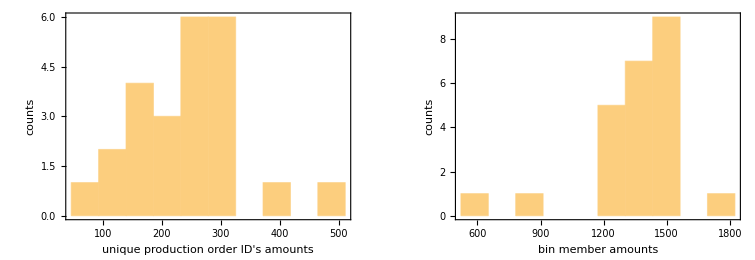

```mathematica
GraphicsRow[{Histogram[KeySort@MapThread[#1->#2&,{Keys@GroupBy[Thread[{productionorder,aim}],Last->First],Table[Length[i],{i,productionorderbasketsrev}]}],{"Raw",10},Frame->True,FrameLabel->{"unique production order ID's amounts","counts"},ImageSize->Full(*,PlotLabel->"Unique Production Order ID Counts for Each Bin"*)],Histogram[KeySort@Counts@aim,{"Raw",10},Frame->True,FrameLabel->{"bin member amounts","counts"},ImageSize->Full(*,PlotLabel->"Total Members Counts for Each Bin"*)]}]
```

```mathematica
AbsoluteTiming[singlesupportvalues=Table[N[Count[Table[MemberQ[i,j],{i,aimbasketsrev}],True]/Length[aimbasketsrev]],{j,binningmembers}];]
pairs=Subsets[binningmembers,{2}];
Dimensions[binningmembers]
Dimensions[pairs]
Dimensions[aimbasketsrev]
AbsoluteTiming[pairsupportvalues=Table[N[Count[Table[SubsetQ[i,j],{i,aimbasketsrev}],True]/
Length[aimbasketsrev]],{j,pairs}];]
```

{0.0283689,Null}

{24,2}

{276,2,2}

{738}

{1.7687,Null}

```mathematica
AbsoluteTiming[liftvalues=pairsupportvalues/(DeleteCases[Flatten@UpperTriangularize[Table[singlesupportvalues[[j]]*singlesupportvalues[[k]],{j,Length[binningmembers]},{k,Length[binningmembers]}],1],0.]);]
```

{0.0008115,Null}

```mathematica
allmatrixelements=Sort[Join[pairs,Reverse[pairs,2],Table[{i,i},{i,binningmembers}]]];
```

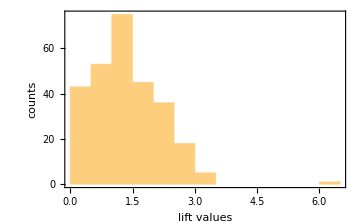

```mathematica
Histogram[liftvalues,PlotRange->All,Frame->True,FrameLabel->{"lift values","counts"},ImageSize->Medium]
```

{180,2,2}

{0.0233476,Null}

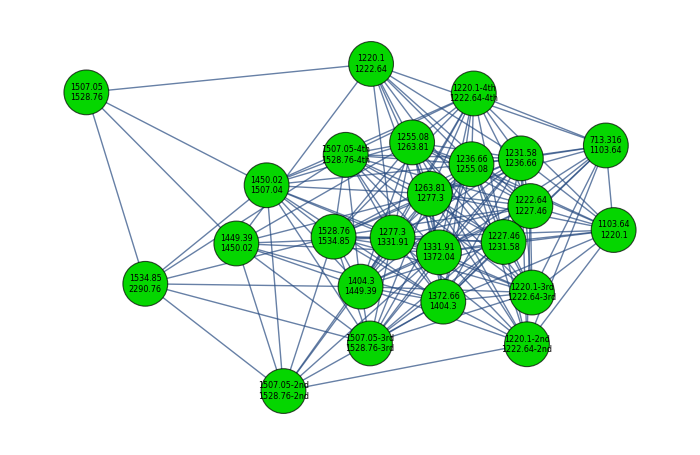

```mathematica
likelypairs=Extract[pairs,Position[liftvalues,x_/;x>1]];
Dimensions@likelypairs
AbsoluteTiming[binarymatrix=ArrayReshape[Table[If[j==True,1,0],{j,Table[MemberQ[likelypairs,i],{i,allmatrixelements}]}],{Length@binningmembers,Length@binningmembers}];]
graph=AdjacencyGraph[binarymatrix,{GraphLayout->Automatic,DirectedEdges->False,EdgeShapeFunction->"Line",VertexSize->1,VertexStyle->RGBColor[0.02,0.84,0.],VertexLabelStyle->Directive[Black,Italic,8],VertexLabels->Flatten[MapThread[{#1->Placed[#2,Center]}&,{Range[1,Dimensions[binarymatrix][[1]]],
Table[StringRiffle[i,"\n"],{i,binningmembers}]}]]},ImageSize->700]
```